```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
vp={50,100,200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000};
fname=Table[ToString[StringForm["point_`1`_Measure_Continuous.csv",vp[[i]]]],{i,Length[vp]}];
```

```mathematica
points=Table[ToExpression[StringSplit[Import[ToString[StringForm["Runs/`1`",fname[[i]]]],"List"][[1]],";"]],{i,Length[fname]}];
```

```mathematica
data=Table[{vp[[i]]/1000,points[[i,1]],points[[i,2]]},{i,Length[vp]}];
```

```mathematica
VpeakFit=LinearModelFit[data[[;;,{1,2}]],x,x,Weights->1/data[[;;,3]]^2,VarianceEstimatorFunction->(1 &)];
```

```mathematica
VpeakListPlot=ErrorListPlot[Table[{{data[[i,1]],data[[i,2]]},ErrorBar[data[[i,3]]]},{i,Length[data]}]];
VpeakFitPlot=Plot[VpeakFit[x],{x,data[[1,1]],data[[-1,1]]},PlotStyle->Red];
```

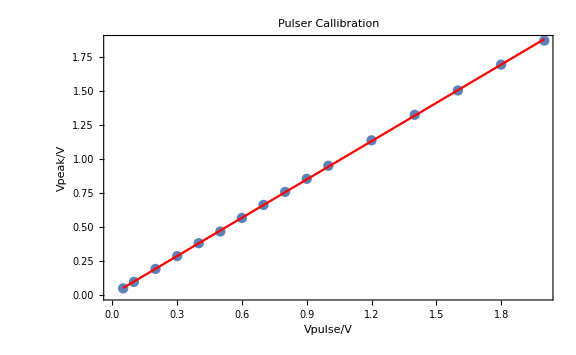

{0.0039646+0.939 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0039646 | 0.000914062 | 4.33734 | 0.000682463
x | 0.939 | 0.000902259 | 1040.72 | 1.26273×10^-35,0.99993,0.999925}

{0.0039646+0.939 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0039646 | 0.000914062 | 4.33734 | 0.000682463
x | 0.939 | 0.000902259 | 1040.72 | 1.26273×10^-35,0.99993,0.999925}

```mathematica
Show[{VpeakListPlot,VpeakFitPlot},ImageSize->Large,PlotLabel->"Pulser Callibration",Frame->{{True,False},{True,False}},FrameLabel->{Vpulse/V,Vpeak/V}]
VpeakFit[{"BestFit","ParameterTable","RSquared","AdjustedRSquared"}]
{0.003964599809177296+0.9389997300192019 x,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 0.003964599809177296, 0.0009140616782914205, 4.337343861289528, 0.000682463203047119}, {x, 0.9389997300192019, 0.0009022593422946808, 1040.7204292627005, 1.2627274832996927*^-35}},0.9999302738170057,0.9999252933753633}
```